# Mathematica 101

## Some simple computations ...

Hello world!

```mathematica
Print["Hello World!"]
```

Hello World!

You can use Mathematica as a calculator (use Shift + Enter to evaluate a cell).

```mathematica
1+1
```

2

You can assign results to variables for later use.

```mathematica
var=1+1
```

2

```mathematica
var^3
```

8

Mathematica data structures are mostly list based.

```mathematica
list={1,2,3,4,5}
```

{1,2,3,4,5}

Most mathematical operators can be used on lists directly.

```mathematica
list/3
```

{1/3,2/3,1,4/3,5/3}

Even matrices are implemented as lists of lists.

```mathematica
matrix={{1,2,3},{4,5,6},{7,8,9}}
```

{{1,2,3},{4,5,6},{7,8,9}}

Calculate the rank of the matrix.

```mathematica
MatrixRank[matrix]
```

2

Calculate the eigenvalues.

```mathematica
Eigenvalues[{{1,2,3},{4,5,6},{7,8,9}}]
```

{3/2 (5+√33),3/2 (5-√33),0}

Formatting functions can be used to make data structures more readable.

```mathematica
MatrixForm[matrix]
TableForm[matrix]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

1 | 2 | 3
4 | 5 | 6
7 | 8 | 9

You can do many things with lists. First, let’s generate a list programmatically using the Range function.

```mathematica
list=Range[1,9]
```

{1,2,3,4,5,6,7,8,9}

The Table function could have been used as well.

```mathematica
Table[i,{i,1,9}]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
Table[i+j,{i,1,3},{j,0,2}]//TableForm
```

1 | 2 | 3
2 | 3 | 4
3 | 4 | 5

Let’s partition the list to regenerate the matrix from the previous example

```mathematica
matrix=Partition[list,3]
MatrixForm[matrix]
```

{{1,2,3},{4,5,6},{7,8,9}}

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

We can flatten the matrix to obtain the original list

```mathematica
Flatten[matrix]
```

{1,2,3,4,5,6,7,8,9}

We can access certain parts of the list or the matrix using the [[]] (Part) operator (the Span operator ;; can be used for slicing)

```mathematica
list[[2]]
list[[-2]]
list[[2;;-2]]
```

2

8

{2,3,4,5,6,7,8}

```mathematica
matrix[[2(*rows*),3(*columns*)]]
matrix[[1;;2(*rows*),3(*columns*)]]
```

6

{3,6}

```mathematica
list
```

{1,2,3,4,5,6,7,8,9}

```mathematica
reverseList=Reverse[list]
```

{9,8,7,6,5,4,3,2,1}

Combining data is easy

```mathematica
Thread[{list,reverseList}]
Thread[list->reverseList]
```

{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}}

{1→9,2→8,3→7,4→6,5→5,6→4,7→3,8→2,9→1}

Exercises

```mathematica
MatrixForm[matrix]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

Sum the diagonal elements of the matrix

```mathematica
(*Put your code here*)
```

Take the dot (Dot) product of the matrix and the list ({a, b, c})

```mathematica
(*Put your code here*)
```

Use the function CoefficientArrays to restore the original matrix from the previously computed equation system.

```mathematica
(*Put your code here*)
```

## Core language

### Conditionals

If statement.

```mathematica
If[2>1,
Print["True"],
Print["False"]
]
```

True

Which statement.

```mathematica
a=2;Which[a==1,x,a==2,b]
```

b

Piecewise statement.

```mathematica
Plot[Piecewise[{{x^2,x<0},{x,x>0}}],{x,-2,2}]
```

### Loops

Iterate over a range of numbers.

```mathematica
Do[Print[i],{i,1,10}]
```

1

2

3

4

5

6

7

8

9

10

Iterate over a range of number constructing a list at the same time

```mathematica
Table[i^i,{i,1,10}]
Table[i^i,{i,1,10,.5}]
```

{1,4,27,256,3125,46656,823543,16777216,387420489,10000000000}

{1.,1.83712,4.,9.88212,27.,80.2118,256.,869.874,3125.,11803.1,46656.,192281.,823543.,3.65561×10^6,1.67772×10^7,7.9444×10^7,3.8742×10^8,1.94256×10^9,1.×10^10}

Iterate over a list of expressions.

```mathematica
colHeaders=ExampleData[{"Statistics","CrabMeasures"},"ColumnDescriptions"]
crabMeasures=ExampleData[{"Statistics","CrabMeasures"}];
crabMeasures//Short
```

{Species - "B" or "O" for blue or orange.,Sex of crab.,Index 1:50 within each of the four groups.,Frontal lobe size (mm).,Rear width (mm).,Carapace length (mm).,Carapace width (mm).,Body depth (mm).}

{{B,M,1,8.1,6.7,16.1,19,7},{B,M,2,8.8,7.7,18.1,20.8,7.4},{B,M,3,9.2,7.8,19,22.4,7.7},«195»,{O,F,49,22.5,17.2,43,48.7,19.8},{O,F,50,23.1,20.2,46.2,52.5,21.1}}

```mathematica
lobeVsRear=Table[{row[[4]],row[[5]]},{row,crabMeasures}]
```

{{8.1,6.7},{8.8,7.7},{9.2,7.8},{9.6,7.9},{9.8,8},{10.8,9},{11.1,9.9},{11.6,9.1},{11.8,9.6},{11.8,10.5},{12.2,10.8},{12.3,11},{12.6,10},{12.8,10.2},{12.8,10.9},{12.9,11},{13.1,10.6},{13.1,10.9},{13.3,11.1},{13.9,11.1},{14.3,11.6},{14.6,11.3},{15,10.9},{15,11.5},{15,11.9},{15.2,12.1},{15.4,11.8},{15.7,12.6},{15.9,12.7},{16.1,11.6},{16.1,12.8},{16.2,13.3},{16.3,12.7},{16.4,13},{16.6,13.5},{16.8,12.8},{16.9,13.2},{17.1,12.6},{17.1,12.7},{17.2,13.5},{17.7,13.6},{17.9,14.1},{18,13.7},{18.8,15.8},{19.3,13.5},{19.3,13.8},{19.7,15.3},{19.8,14.2},{19.8,14.3},{21.3,15.7},{7.2,6.5},{9,8.5},{9.1,8.1},{9.1,8.2},{9.5,8.2},{9.8,8.9},{10.1,9.3},{10.3,9.5},{10.4,9.7},{10.8,9.5},{11,9.8},{11.2,10},{11.5,11},{11.6,11},{11.6,11.4},{11.7,10.6},{11.9,11.4},{12,10.7},{12,11.1},{12.6,12.2},{12.8,11.7},{12.8,12.2},{12.8,12.2},{13,11.4},{13.1,11.5},{13.2,12.2},{13.4,11.8},{13.7,12.5},{13.9,13},{14.7,12.5},{14.9,13.2},{15,13.8},{15,14.2},{15.1,13.3},{15.1,13.5},{15.1,13.8},{15.2,14.3},{15.3,14.2},{15.4,13.3},{15.5,13.8},{15.6,13.9},{15.6,14.7},{15.7,13.9},{15.8,15},{16.2,15.2},{16.4,14},{16.7,16.1},{17.4,16.9},{17.5,16.7},{19.2,16.5},{9.1,6.9},{10.2,8.2},{10.7,8.6},{11.4,9},{12.5,9.4},{12.5,9.4},{12.7,10.4},{13.2,11},{13.4,10.1},{13.7,11},{14,11.5},{14.1,10.4},{14.1,10.5},{14.1,10.7},{14.2,10.6},{14.2,10.7},{14.2,11.3},{14.6,11.3},{14.7,11.1},{15.1,11.4},{15.1,11.5},{15.4,11.1},{15.7,12.2},{16.2,11.8},{16.3,11.6},{17.1,12.6},{17.4,12.8},{17.5,12},{17.5,12.7},{17.8,12.5},{17.9,12.9},{18,13.4},{18.2,13.7},{18.4,13.4},{18.6,13.4},{18.6,13.5},{18.8,13.4},{18.8,13.8},{19.4,14.1},{19.4,14.4},{20.1,13.7},{20.6,14.4},{21,15},{21.5,15.5},{21.6,15.4},{21.6,14.8},{21.9,15.7},{22.1,15.8},{23,16.8},{23.1,15.7},{10.7,9.7},{11.4,9.2},{12.5,10},{12.6,11.5},{12.9,11.2},{14,11.9},{14,12.8},{14.3,12.2},{14.7,13.2},{14.9,13},{15,12.3},{15.6,13.5},{15.6,14},{15.6,14.1},{15.7,13.6},{16.1,13.6},{16.1,13.7},{16.2,14},{16.7,14.3},{17.1,14.5},{17.5,14.3},{17.5,14.4},{17.5,14.7},{17.6,14},{18,14.9},{18,16.3},{18.3,15.7},{18.4,15.5},{18.4,15.7},{18.5,14.6},{18.6,14.5},{18.8,15.2},{18.9,16.7},{19.1,16},{19.1,16.3},{19.7,16.7},{19.9,16.6},{19.9,17.9},{20,16.7},{20.1,17.2},{20.3,16},{20.5,17.5},{20.6,17.5},{20.9,16.5},{21.3,18.4},{21.4,18},{21.7,17.1},{21.9,17.2},{22.5,17.2},{23.1,20.2}}

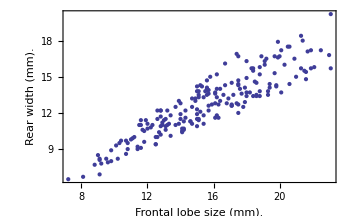

```mathematica
ListPlot[lobeVsRear,FrameLabel->colHeaders[[{4,5}]]]
```

Iterate in multiple dimensions.

```mathematica
Table[i+j,{i,1,10},{j,1,10}]
TableForm[%]
```

{{2,3,4,5,6,7,8,9,10,11},{3,4,5,6,7,8,9,10,11,12},{4,5,6,7,8,9,10,11,12,13},{5,6,7,8,9,10,11,12,13,14},{6,7,8,9,10,11,12,13,14,15},{7,8,9,10,11,12,13,14,15,16},{8,9,10,11,12,13,14,15,16,17},{9,10,11,12,13,14,15,16,17,18},{10,11,12,13,14,15,16,17,18,19},{11,12,13,14,15,16,17,18,19,20}}

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

Loop until a condition become untrue.

```mathematica
While[(rnd=RandomReal[])<.8,Print[rnd]]
```

0.410211

0.618

0.441564

0.401222

0.430969

0.36209

0.312197

## Mathematica caveats and how to avoid them

### You have to be aware of the fact that the order of evaluation is not preserved in a Notebook environment. That is a cool feature in a prototyping setting but can lead to non-trivial errors, responsible for most of the voodoo going on

```mathematica
a=1;
b=2;
```

```mathematica
a/b
```

1/2

```mathematica
b=0
```

0

### Quiting the kernel (using either the menu, Evaluation -> Quit Kernel or the function Quit[]) helps resolving those issues. Encapsulating code into functions and avoiding lots of variables assignments helps too.

```mathematica
Quit[]
```

```mathematica
a=1
```

1

```mathematica
a
```

1

```mathematica
a=1
```

1

```mathematica
a="string"
```

string

```mathematica
a
```

string

### Previous definitions of a variable can be erased using Clear[var1, ...]

```mathematica
a=1
```

1

```mathematica
a
```

1

```mathematica
a
```

1

```mathematica
Clear[a]
```

```mathematica
a
```

a

### Instead of quitting the Kernel one clear all variables of a certain Context (a.k.a. namespace)

```mathematica
a=1
```

1

```mathematica
Context[a]
```

Global`

```mathematica
niko`a=3
```

3

```mathematica
Context[niko`a]
```

niko`

```mathematica
Clear["Global`*"]
```

```mathematica
a
niko`a
```

a

3

## Everything is an expression ...

### Many expressions are rendered and entered using special syntax and notation. However, internally they look all the same (head[args...]). This can be made visible using the Function FullForm. In this way Mathematica is very similar to functional programming languages like Lisp, Scheme etc, e.g., (operator arg1 arg2 arg3 ...) -> (+ 1 2 3).

```mathematica
{1,2,3}
1->3
1/3
"1/3"
```

{1,2,3}

1→3

1/3

1/3

```mathematica
FullForm[{1,2,3}]
FullForm[1->3]
FullForm[1/3]
FullForm["1/3"]
```

List[1,2,3]

Rule[1,3]

Rational[1,3]

"1/3"

### Use Head to get the head of an expression

```mathematica
Head[{1,2,3}]
Head[3.]
Head[1/3]
Head["1/3"]
```

List

Real

Rational

String

### Changing the Head of an expression using Apply (@@)

```mathematica
NewHead@@{1,2,3}
Apply[NewHead,{1,2,3}]
```

NewHead[1,2,3]

NewHead[1,2,3]

```mathematica
Plus@@{a,b,c}
Times@@{a,b,c}
Power@@{a,b,c}
```

a+b+c

a b c

a^(b^c)

```mathematica
Plus@@{1,2,3}
Times@@{1,2,3}
Power@@{1,2,3}
```

6

6

1

## Mathematica patterns and rule-based programming

### What are patterns (patternID_Head)? Think of them as some kind of ‘regular expressions’ but for all kinds of expressions.

### A _ represents a pattern that matches any expression

```mathematica
_
```

```mathematica
MatchQ[1,_String]
MatchQ[1.,_String]
MatchQ["one",_String]
```

False

False

True

```mathematica
MatchQ["one",_String]
```

```mathematica
#->MatchQ[#,_]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→True,1.→True,String→True,1/3→True,{1,2,3,4}→True}

### How to construct a pattern (_) that matches only certain expressions?

```mathematica
#->MatchQ[#,_String]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→False,1.→False,String→True,1/3→False,{1,2,3,4}→False}

```mathematica
#->MatchQ[#,_Rational]&/@{1,1.,"String",1/3,{1,2,3,4}}
```

{1→False,1.→False,String→False,1/3→True,{1,2,3,4}→False}

### Conditional patterns (pattern_ /; Condition[pattern] )

```mathematica
Head[4.]
```

Real

```mathematica
Cases[{{1,2,3,4.},{1,2,3}},l_List/;Length[l]≥4&&MemberQ[l,88.]]
```

{}

### Matching a sequence of expressions

#### Matching a bunch of Integers in a list

```mathematica
MatchQ[{1,2,3,4},{__Integer}]
```

#### They have to be all integers

```mathematica
MatchQ[{1,2,3,4.},{__Integer}]
```

#### There has to be at least on integer present

```mathematica
MatchQ[{},{__Integer}]
```

#### ___Integer matches 0 or more integers

```mathematica
MatchQ[{},{___Integer}]
```

### Some neat functions that utilize patterns

```mathematica
Cases[{1,2,3,4.},_Real]
```

{4.}

```mathematica
Count[{1,2,3,4.},_Real]
```

1

```mathematica
Cases[{{1,2,3,4.}},_Real]
```

{}

```mathematica
Cases[{{1,2,3,4.}},_Real,Infinity]
```

{4.}

### Rule-based programming

```mathematica
{1,2,3,4.}/.i_Real/;i>2:>i^2
```

{1,2,3,16.}

```mathematica
FullForm[Hold[{1,2,3,4}/.i_/;i>2:>i^2]]
```

Hold[ReplaceAll[List[1,2,3,4],RuleDelayed[Condition[Pattern[i,Blank[]],Greater[i,2]],Power[i,2]]]]

## Defining functions

### Divide & Conquer: encapsulate your stuff into Mathematica functions.

Always ...
1. Localize all local variables (using Module)!
2. Never, ever, use global variables!
3. Use strongly typed arguments and check user input (which is pretty easy as patterns are used to specify arguments)!
4. Abort evaluation (and provide a meaningful message) if user input does not match the function’s argument signature

```mathematica
Unprotect[function];
function::wrngargs="Provided arguments don't match any definition of function";
function[arg1_Integer,arg2_List]:=Module[{localVariable},
localVariable=arg1+2;
localVariable+arg2
];
function[arg1_Real,arg2_List]:=Module[{localVariable},
localVariable=arg1+2;
localVariable/arg2
];
function[___]:=(Message[function::wrngargs];Abort[])
Protect[function];
```

```mathematica
function[1,{1,2,3}]
```

{4,5,6}

```mathematica
function[1.,{1,2,3}]
function[1.]
function[1,{1,2,3},3.]
```

{3.,1.5,1.}

function::wrngargs: Provided arguments don't match any definition of function

$Aborted

function::wrngargs: Provided arguments don't match any definition of function

$Aborted

```mathematica
function=1
```

Set::wrsym: Symbol function is Protected.

1

Define a function that ...

```mathematica
1+1
```

Put some stuff here

### Lambda functions (λ calculus; anonymous functions; good for quick hacks ...)

#### The slot symbol # represents an argument

```mathematica
#&[2] (*Same as lambda x: x in python*)
```

2

```mathematica
#^2&[2](*Same as lambda x: x**2 in python*)
```

4

#### #2 represents the second argument provided

```mathematica
#1^#2&[2,3] (*Same as lambda x,y: x**y *)
```

8

### Applying functions to expressions ...

#### Map (/@)

```mathematica
function[#[[1]],#[[2]]]&/@{{1.,{1,2,3}},{2.,{2,3,4}}}
```

{{1,{1,2,3}},{2,{2,3,4}}}

{function[1.,{1,2,3}],function[2.,{2,3,4}]}

#### Select

```mathematica
Select[{1,2,3,4,5},OddQ]
```

{1,3,5}

Define a lambda function that will let Select filter numbers

```mathematica
ExampleData[{"Statistics","DNaseAssay"},"ColumnDescriptions"]
```

{Index for assay run.,Concentration of the protein.,Dimensionless measure of optical density.}

```mathematica
dnaseAssay=ExampleData[{"Statistics","DNaseAssay"}]
```

{{1,0.0488281,0.017},{1,0.0488281,0.018},{1,0.195313,0.121},{1,0.195313,0.124},{1,0.390625,0.206},{1,0.390625,0.215},{1,0.78125,0.377},{1,0.78125,0.374},{1,1.5625,0.614},{1,1.5625,0.609},{1,3.125,1.019},{1,3.125,1.001},{1,6.25,1.334},{1,6.25,1.364},{1,12.5,1.73},{1,12.5,1.71},{2,0.0488281,0.045},{2,0.0488281,0.05},{2,0.195313,0.137},{2,0.195313,0.123},{2,0.390625,0.225},{2,0.390625,0.207},{2,0.78125,0.401},{2,0.78125,0.383},{2,1.5625,0.672},{2,1.5625,0.681},{2,3.125,1.116},{2,3.125,1.078},{2,6.25,1.554},{2,6.25,1.526},{2,12.5,1.932},{2,12.5,1.914},{3,0.0488281,0.07},{3,0.0488281,0.068},{3,0.195313,0.173},{3,0.195313,0.165},{3,0.390625,0.277},{3,0.390625,0.248},{3,0.78125,0.434},{3,0.78125,0.426},{3,1.5625,0.703},{3,1.5625,0.689},{3,3.125,1.067},{3,3.125,1.077},{3,6.25,1.629},{3,6.25,1.479},{3,12.5,2.003},{3,12.5,1.884},{4,0.0488281,0.011},{4,0.0488281,0.016},{4,0.195313,0.118},{4,0.195313,0.108},{4,0.390625,0.2},{4,0.390625,0.206},{4,0.78125,0.364},{4,0.78125,0.36},{4,1.5625,0.62},{4,1.5625,0.64},{4,3.125,0.979},{4,3.125,0.973},{4,6.25,1.424},{4,6.25,1.399},{4,12.5,1.74},{4,12.5,1.732},{5,0.0488281,0.035},{5,0.0488281,0.035},{5,0.195313,0.132},{5,0.195313,0.135},{5,0.390625,0.224},{5,0.390625,0.22},{5,0.78125,0.385},{5,0.78125,0.39},{5,1.5625,0.658},{5,1.5625,0.647},{5,3.125,1.06},{5,3.125,1.031},{5,6.25,1.425},{5,6.25,1.409},{5,12.5,1.75},{5,12.5,1.738},{6,0.0488281,0.086},{6,0.0488281,0.103},{6,0.195313,0.191},{6,0.195313,0.189},{6,0.390625,0.272},{6,0.390625,0.277},{6,0.78125,0.44},{6,0.78125,0.426},{6,1.5625,0.686},{6,1.5625,0.676},{6,3.125,1.062},{6,3.125,1.072},{6,6.25,1.424},{6,6.25,1.459},{6,12.5,1.768},{6,12.5,1.806},{7,0.0488281,0.094},{7,0.0488281,0.092},{7,0.195313,0.182},{7,0.195313,0.182},{7,0.390625,0.282},{7,0.390625,0.273},{7,0.78125,0.444},{7,0.78125,0.439},{7,1.5625,0.686},{7,1.5625,0.668},{7,3.125,1.052},{7,3.125,1.035},{7,6.25,1.409},{7,6.25,1.392},{7,12.5,1.759},{7,12.5,1.739},{8,0.0488281,0.054},{8,0.0488281,0.054},{8,0.195313,0.152},{8,0.195313,0.148},{8,0.390625,0.226},{8,0.390625,0.222},{8,0.78125,0.392},{8,0.78125,0.383},{8,1.5625,0.658},{8,1.5625,0.644},{8,3.125,1.043},{8,3.125,1.002},{8,6.25,1.466},{8,6.25,1.381},{8,12.5,1.743},{8,12.5,1.724},{9,0.0488281,0.032},{9,0.0488281,0.043},{9,0.195313,0.142},{9,0.195313,0.155},{9,0.390625,0.239},{9,0.390625,0.242},{9,0.78125,0.42},{9,0.78125,0.395},{9,1.5625,0.624},{9,1.5625,0.705},{9,3.125,1.046},{9,3.125,1.026},{9,6.25,1.398},{9,6.25,1.405},{9,12.5,1.693},{9,12.5,1.729},{10,0.0488281,0.052},{10,0.0488281,0.094},{10,0.195313,0.164},{10,0.195313,0.166},{10,0.390625,0.259},{10,0.390625,0.256},{10,0.78125,0.439},{10,0.78125,0.439},{10,1.5625,0.69},{10,1.5625,0.701},{10,3.125,1.042},{10,3.125,1.075},{10,6.25,1.34},{10,6.25,1.406},{10,12.5,1.699},{10,12.5,1.708},{11,0.0488281,0.047},{11,0.0488281,0.057},{11,0.195313,0.159},{11,0.195313,0.155},{11,0.390625,0.246},{11,0.390625,0.252},{11,0.78125,0.427},{11,0.78125,0.411},{11,1.5625,0.704},{11,1.5625,0.684},{11,3.125,0.994},{11,3.125,0.98},{11,6.25,1.421},{11,6.25,1.385},{11,12.5,1.715},{11,12.5,1.721}}

```mathematica
Cases[dnaseAssay,{#,__}]&/@Union[dnaseAssay[[All,1]]]
```

{{{1,0.0488281,0.017},{1,0.0488281,0.018},{1,0.195313,0.121},{1,0.195313,0.124},{1,0.390625,0.206},{1,0.390625,0.215},{1,0.78125,0.377},{1,0.78125,0.374},{1,1.5625,0.614},{1,1.5625,0.609},{1,3.125,1.019},{1,3.125,1.001},{1,6.25,1.334},{1,6.25,1.364},{1,12.5,1.73},{1,12.5,1.71}},{{2,0.0488281,0.045},{2,0.0488281,0.05},{2,0.195313,0.137},{2,0.195313,0.123},{2,0.390625,0.225},{2,0.390625,0.207},{2,0.78125,0.401},{2,0.78125,0.383},{2,1.5625,0.672},{2,1.5625,0.681},{2,3.125,1.116},{2,3.125,1.078},{2,6.25,1.554},{2,6.25,1.526},{2,12.5,1.932},{2,12.5,1.914}},{{3,0.0488281,0.07},{3,0.0488281,0.068},{3,0.195313,0.173},{3,0.195313,0.165},{3,0.390625,0.277},{3,0.390625,0.248},{3,0.78125,0.434},{3,0.78125,0.426},{3,1.5625,0.703},{3,1.5625,0.689},{3,3.125,1.067},{3,3.125,1.077},{3,6.25,1.629},{3,6.25,1.479},{3,12.5,2.003},{3,12.5,1.884}},{{4,0.0488281,0.011},{4,0.0488281,0.016},{4,0.195313,0.118},{4,0.195313,0.108},{4,0.390625,0.2},{4,0.390625,0.206},{4,0.78125,0.364},{4,0.78125,0.36},{4,1.5625,0.62},{4,1.5625,0.64},{4,3.125,0.979},{4,3.125,0.973},{4,6.25,1.424},{4,6.25,1.399},{4,12.5,1.74},{4,12.5,1.732}},{{5,0.0488281,0.035},{5,0.0488281,0.035},{5,0.195313,0.132},{5,0.195313,0.135},{5,0.390625,0.224},{5,0.390625,0.22},{5,0.78125,0.385},{5,0.78125,0.39},{5,1.5625,0.658},{5,1.5625,0.647},{5,3.125,1.06},{5,3.125,1.031},{5,6.25,1.425},{5,6.25,1.409},{5,12.5,1.75},{5,12.5,1.738}},{{6,0.0488281,0.086},{6,0.0488281,0.103},{6,0.195313,0.191},{6,0.195313,0.189},{6,0.390625,0.272},{6,0.390625,0.277},{6,0.78125,0.44},{6,0.78125,0.426},{6,1.5625,0.686},{6,1.5625,0.676},{6,3.125,1.062},{6,3.125,1.072},{6,6.25,1.424},{6,6.25,1.459},{6,12.5,1.768},{6,12.5,1.806}},{{7,0.0488281,0.094},{7,0.0488281,0.092},{7,0.195313,0.182},{7,0.195313,0.182},{7,0.390625,0.282},{7,0.390625,0.273},{7,0.78125,0.444},{7,0.78125,0.439},{7,1.5625,0.686},{7,1.5625,0.668},{7,3.125,1.052},{7,3.125,1.035},{7,6.25,1.409},{7,6.25,1.392},{7,12.5,1.759},{7,12.5,1.739}},{{8,0.0488281,0.054},{8,0.0488281,0.054},{8,0.195313,0.152},{8,0.195313,0.148},{8,0.390625,0.226},{8,0.390625,0.222},{8,0.78125,0.392},{8,0.78125,0.383},{8,1.5625,0.658},{8,1.5625,0.644},{8,3.125,1.043},{8,3.125,1.002},{8,6.25,1.466},{8,6.25,1.381},{8,12.5,1.743},{8,12.5,1.724}},{{9,0.0488281,0.032},{9,0.0488281,0.043},{9,0.195313,0.142},{9,0.195313,0.155},{9,0.390625,0.239},{9,0.390625,0.242},{9,0.78125,0.42},{9,0.78125,0.395},{9,1.5625,0.624},{9,1.5625,0.705},{9,3.125,1.046},{9,3.125,1.026},{9,6.25,1.398},{9,6.25,1.405},{9,12.5,1.693},{9,12.5,1.729}},{{10,0.0488281,0.052},{10,0.0488281,0.094},{10,0.195313,0.164},{10,0.195313,0.166},{10,0.390625,0.259},{10,0.390625,0.256},{10,0.78125,0.439},{10,0.78125,0.439},{10,1.5625,0.69},{10,1.5625,0.701},{10,3.125,1.042},{10,3.125,1.075},{10,6.25,1.34},{10,6.25,1.406},{10,12.5,1.699},{10,12.5,1.708}},{{11,0.0488281,0.047},{11,0.0488281,0.057},{11,0.195313,0.159},{11,0.195313,0.155},{11,0.390625,0.246},{11,0.390625,0.252},{11,0.78125,0.427},{11,0.78125,0.411},{11,1.5625,0.704},{11,1.5625,0.684},{11,3.125,0.994},{11,3.125,0.98},{11,6.25,1.421},{11,6.25,1.385},{11,12.5,1.715},{11,12.5,1.721}}}

```mathematica
GatherBy[dnaseAssay,#[[1]]&][[All,All,2;;3]]
```

{{{0.0488281,0.017},{0.0488281,0.018},{0.195313,0.121},{0.195313,0.124},{0.390625,0.206},{0.390625,0.215},{0.78125,0.377},{0.78125,0.374},{1.5625,0.614},{1.5625,0.609},{3.125,1.019},{3.125,1.001},{6.25,1.334},{6.25,1.364},{12.5,1.73},{12.5,1.71}},{{0.0488281,0.045},{0.0488281,0.05},{0.195313,0.137},{0.195313,0.123},{0.390625,0.225},{0.390625,0.207},{0.78125,0.401},{0.78125,0.383},{1.5625,0.672},{1.5625,0.681},{3.125,1.116},{3.125,1.078},{6.25,1.554},{6.25,1.526},{12.5,1.932},{12.5,1.914}},{{0.0488281,0.07},{0.0488281,0.068},{0.195313,0.173},{0.195313,0.165},{0.390625,0.277},{0.390625,0.248},{0.78125,0.434},{0.78125,0.426},{1.5625,0.703},{1.5625,0.689},{3.125,1.067},{3.125,1.077},{6.25,1.629},{6.25,1.479},{12.5,2.003},{12.5,1.884}},{{0.0488281,0.011},{0.0488281,0.016},{0.195313,0.118},{0.195313,0.108},{0.390625,0.2},{0.390625,0.206},{0.78125,0.364},{0.78125,0.36},{1.5625,0.62},{1.5625,0.64},{3.125,0.979},{3.125,0.973},{6.25,1.424},{6.25,1.399},{12.5,1.74},{12.5,1.732}},{{0.0488281,0.035},{0.0488281,0.035},{0.195313,0.132},{0.195313,0.135},{0.390625,0.224},{0.390625,0.22},{0.78125,0.385},{0.78125,0.39},{1.5625,0.658},{1.5625,0.647},{3.125,1.06},{3.125,1.031},{6.25,1.425},{6.25,1.409},{12.5,1.75},{12.5,1.738}},{{0.0488281,0.086},{0.0488281,0.103},{0.195313,0.191},{0.195313,0.189},{0.390625,0.272},{0.390625,0.277},{0.78125,0.44},{0.78125,0.426},{1.5625,0.686},{1.5625,0.676},{3.125,1.062},{3.125,1.072},{6.25,1.424},{6.25,1.459},{12.5,1.768},{12.5,1.806}},{{0.0488281,0.094},{0.0488281,0.092},{0.195313,0.182},{0.195313,0.182},{0.390625,0.282},{0.390625,0.273},{0.78125,0.444},{0.78125,0.439},{1.5625,0.686},{1.5625,0.668},{3.125,1.052},{3.125,1.035},{6.25,1.409},{6.25,1.392},{12.5,1.759},{12.5,1.739}},{{0.0488281,0.054},{0.0488281,0.054},{0.195313,0.152},{0.195313,0.148},{0.390625,0.226},{0.390625,0.222},{0.78125,0.392},{0.78125,0.383},{1.5625,0.658},{1.5625,0.644},{3.125,1.043},{3.125,1.002},{6.25,1.466},{6.25,1.381},{12.5,1.743},{12.5,1.724}},{{0.0488281,0.032},{0.0488281,0.043},{0.195313,0.142},{0.195313,0.155},{0.390625,0.239},{0.390625,0.242},{0.78125,0.42},{0.78125,0.395},{1.5625,0.624},{1.5625,0.705},{3.125,1.046},{3.125,1.026},{6.25,1.398},{6.25,1.405},{12.5,1.693},{12.5,1.729}},{{0.0488281,0.052},{0.0488281,0.094},{0.195313,0.164},{0.195313,0.166},{0.390625,0.259},{0.390625,0.256},{0.78125,0.439},{0.78125,0.439},{1.5625,0.69},{1.5625,0.701},{3.125,1.042},{3.125,1.075},{6.25,1.34},{6.25,1.406},{12.5,1.699},{12.5,1.708}},{{0.0488281,0.047},{0.0488281,0.057},{0.195313,0.159},{0.195313,0.155},{0.390625,0.246},{0.390625,0.252},{0.78125,0.427},{0.78125,0.411},{1.5625,0.704},{1.5625,0.684},{3.125,0.994},{3.125,0.98},{6.25,1.421},{6.25,1.385},{12.5,1.715},{12.5,1.721}}}

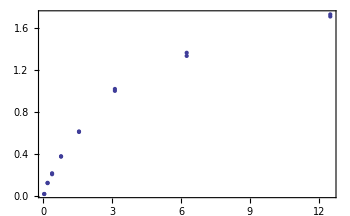

```mathematica
ListPlot[Select[dnaseAssay,#[[1]]==1&][[All,2;;]]]
```

```mathematica
ListPlot[Select[dnaseAssay,#[[1]]==1&][[All,2;;]]]
```

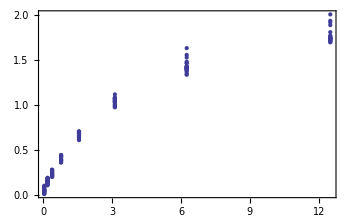

```mathematica
ListPlot[ExampleData[{"Statistics","DNaseAssay"}][[All,2;;]],PlotRange->All]
```

```mathematica
colHeaders=ExampleData[{"Statistics","CrabMeasures"},"ColumnDescriptions"]
crabMeasures=ExampleData[{"Statistics","CrabMeasures"}];
crabMeasures//Short
```

{Species - "B" or "O" for blue or orange.,Sex of crab.,Index 1:50 within each of the four groups.,Frontal lobe size (mm).,Rear width (mm).,Carapace length (mm).,Carapace width (mm).,Body depth (mm).}

{{B,M,1,8.1,6.7,16.1,19,7},{B,M,2,8.8,7.7,18.1,20.8,7.4},{B,M,3,9.2,7.8,19,22.4,7.7},«195»,{O,F,49,22.5,17.2,43,48.7,19.8},{O,F,50,23.1,20.2,46.2,52.5,21.1}}

```mathematica
SetDirectory[NotebookDirectory[]];
gffData=Import["data/Transcripts.gff3"]
```

{{edit_test.fa,.,gene,500,2610,.,+,.,ID=newGene},{edit_test.fa,.,mRNA,500,2385,.,+,.,Parent=newGene;Namo=reinhard+did+this;Name=t1%28newGene%29;ID=t1;uri=http%3A//www.yahoo.com},{edit_test.fa,.,five_prime_UTR,500,802,.,+,.,Parent=t1},{edit_test.fa,.,CDS,803,1012,.,+,.,Parent=t1},{edit_test.fa,.,three_prime_UTR,1013,1168,.,+,.,Parent=t1},{edit_test.fa,.,three_prime_UTR,1475,1654,.,+,.,Parent=t1},{edit_test.fa,.,three_prime_UTR,1720,1908,.,+,.,Parent=t1},{edit_test.fa,.,three_prime_UTR,2047,2385,.,+,.,Parent=t1},{edit_test.fa,.,mRNA,1050,2610,.,+,.,Parent=newGene;Name=t2%28newGene%29;ID=t2},{edit_test.fa,.,CDS,1050,1196,.,+,.,Parent=t2},{edit_test.fa,.,CDS,1472,1651,.,+,.,Parent=t2},{edit_test.fa,.,CDS,1732,2610,.,+,.,Parent=t2},{edit_test.fa,.,mRNA,1050,2610,.,+,.,Parent=newGene;Name=t3%28newGene%29;ID=t3},{edit_test.fa,.,CDS,1050,1196,.,+,.,Parent=t3},{edit_test.fa,.,CDS,1472,1651,.,+,.,Parent=t3},{edit_test.fa,.,CDS,1732,2610,.,+,.,Parent=t3}}

```mathematica
"edit_test.fa",".","mRNA",1050,2610,".","+",".","Parent=newGene;Name=t3%28newGene%29;ID=t3"
```

```mathematica
gffData//TableForm
```

edit_test.fa | . | gene | 500 | 2610 | . | + | . | ID=newGene
edit_test.fa | . | mRNA | 500 | 2385 | . | + | . | Parent=newGene;Namo=reinhard+did+this;Name=t1%28newGene%29;ID=t1;uri=http%3A//www.yahoo.com
edit_test.fa | . | five_prime_UTR | 500 | 802 | . | + | . | Parent=t1
edit_test.fa | . | CDS | 803 | 1012 | . | + | . | Parent=t1
edit_test.fa | . | three_prime_UTR | 1013 | 1168 | . | + | . | Parent=t1
edit_test.fa | . | three_prime_UTR | 1475 | 1654 | . | + | . | Parent=t1
edit_test.fa | . | three_prime_UTR | 1720 | 1908 | . | + | . | Parent=t1
edit_test.fa | . | three_prime_UTR | 2047 | 2385 | . | + | . | Parent=t1
edit_test.fa | . | mRNA | 1050 | 2610 | . | + | . | Parent=newGene;Name=t2%28newGene%29;ID=t2
edit_test.fa | . | CDS | 1050 | 1196 | . | + | . | Parent=t2
edit_test.fa | . | CDS | 1472 | 1651 | . | + | . | Parent=t2
edit_test.fa | . | CDS | 1732 | 2610 | . | + | . | Parent=t2
edit_test.fa | . | mRNA | 1050 | 2610 | . | + | . | Parent=newGene;Name=t3%28newGene%29;ID=t3
edit_test.fa | . | CDS | 1050 | 1196 | . | + | . | Parent=t3
edit_test.fa | . | CDS | 1472 | 1651 | . | + | . | Parent=t3
edit_test.fa | . | CDS | 1732 | 2610 | . | + | . | Parent=t3

```mathematica
Select[gffData,#[[3]]=="mRNA"&&#[[4]]>500&]//TableForm
```

edit_test.fa | . | mRNA | 1050 | 2610 | . | + | . | Parent=newGene;Name=t2%28newGene%29;ID=t2
edit_test.fa | . | mRNA | 1050 | 2610 | . | + | . | Parent=newGene;Name=t3%28newGene%29;ID=t3

```mathematica
Select[Range[1,100],(*...PUT YOUR FUNCTION HERE...*)]
```

## General tips

### Use the documentation system (Context menu -> Get Help)

```mathematica
NDSolve
```

### Keyboard shortcuts

Cmd + Alt + ]

Cmd + Alt + Shift + }

### Avoid writing C code in Mathematica. Use rule-based programming, functional programming, constructs like Map, Apply, etc., lambda functions ...

```mathematica
stuff={};
For[i=0,i<4,i++,
AppendTo[stuff,i]
];
```

```mathematica
stuff=Table[i,{i,0,3}]
```

{0,1,2,3}

### Use only lowercase variable and function names (uppercase is reserved for Mathematica built-ins)

### Many Mathematica functions allow for flexibility by providing Options. A set of default options is used if the user is not specific. For example, many plotting functions work in that way.

#### Look up a function’s set of available options

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

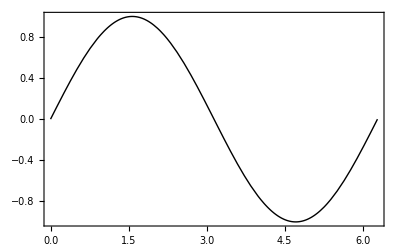

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle->Black,Frame->True,Axes->False]
```

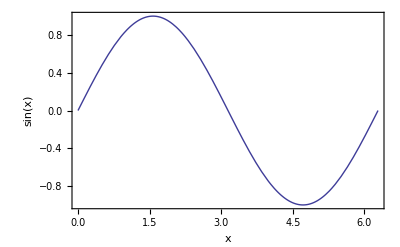

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"}]
```

#### You can change the options of a functions globally. This helps a lot in avoiding redundant code

```mathematica
SetOptions[Plot,Frame->True,LabelStyle->{FontSize->12,FontFamily->"Helvetica"}];
```

```mathematica
Plot[Sin[x],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"}]
```

-Graphics-

### Using Mathematica’s dynamic capabilities to see how results change with varying parameters

```mathematica
Manipulate[
Plot[Sin[x*freq+phase],{x,0,2Pi},Frame->True,FrameLabel->{"x","sin(x)"},ImageSize->300,PlotRange->{All,{-2,2}}],{freq,1,10},{phase,0,2π}]
```

### Check out http://demonstrations.wolfram.com/ for more examples

### Parallelize computations by using ParallelTable, ParallelDo etc.

```mathematica
AbsoluteTiming[
Table[
Eigenvalues[RandomReal[{0,1},{100,100}]]
,{100}
];
]
```

{1.26719,Null}

```mathematica
AbsoluteTiming[
ParallelTable[
Eigenvalues[RandomReal[{0,1},{100,100}]]
,{100}
];
]
```

{0.692283,Null}

## More resources

Best resource and tutorial collection ever